```mathematica
data={{1000,1.1},{2000,2.2},{3000,3.5},{4000,3.7},{5000,5.1}};
line=Fit[data,{1,x,x^2},x]
```

0.02+0.00116429 x-3.57143×10^-8 x^2

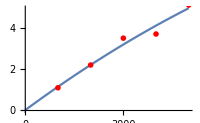
-Graphics-
线性拟合数据

```mathematica
Column[{Plot[line,{x,0,5000},Epilog->{Red,PointSize[0.02],Point/@data},ImageSize->200
],Text@Style["线性拟合数据"]},Alignment->Center]
```

```mathematica
SeedRandom[134]
```

```mathematica
data=Table[{x,x^2+2x+RandomReal[10]},{x,10}];
two=LinearModelFit[data,{x^2,x,1},x]
```

FittedModel[11.9278-0.58209 x+1.19142 x^2]

Plot::optx: Plot[two,{x,0,10},Epilog→{Blue,PointSize[0.02],Point/@data},ImageSize→300,PlotMarkers→Automatic] 中的未知选项 PlotMarkers→Automatic.

Plot[two,{x,0,10},Epilog→{Blue,PointSize[0.02],Point/@data},ImageSize→300,PlotMarkers→Automatic]
二次的拟合曲线

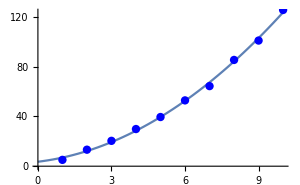
-Graphics-
二次的拟合曲线

```mathematica
Column[{Plot[two,{x,0,10},Epilog->{Blue,PointSize[0.02],Point/@data},ImageSize->300],Text["二次的拟合曲线"]},Alignment->Center]
```

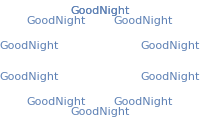

```mathematica
data1=Table[{2 Sin[θ],2Cos[θ]},{θ,0,2π,π/5}];
ListPlot[data1,Axes->False,Frame->False,PlotMarkers->{"GoodNight"},ImageSize->200,ColorFunction->"Rainbow"]
```

```mathematica
testData=Prime[Range[25]];
Manipulate[ListPlot[testData,PlotMarkers->"⌘",PlotStyle->RGBColor[r,g,b]],{r,0,1,Appearance->"Labeled"},{g,0,1,Appearance->"Labeled"},{b,0,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
⌘
```

```mathematica
{{a,b},{c,d},{a}}/.List->Sequence
```

Sequence[a,b,c,d,a]

```mathematica
two["ParameterConfidenceIntervals"]
```

{{0.872282,1.51056},{-4.18429,3.02011},{3.3027,20.5529}}

```mathematica
styletable[tb1_]:=tb1;
tables=Column[styletable[#,{FontSize->11,FontFamily->"Comic Sans MS"}]&/@two[{"ParameterTable","ANOVATable"}],Frame->All];
Column[{Text@Style["参数表格和方差分析表格"],tables},Alignment->Center]
```

参数表格和方差分析表格
 | Estimate | Standard Error | t-Statistic | P-Value
x^2 | 1.19142 | 0.134965 | 8.82766 | 0.000048365
x | -0.58209 | 1.52337 | -0.382107 | 0.713718
1 | 11.9278 | 3.64755 | 3.27008 | 0.0136728
 | DF | SS | MS | F-Statistic | P-Value
x | 1 | 13585.9 | 13585.9 | 1412.58 | 2.45497×10^-9
1 | 1 | 102.847 | 102.847 | 10.6934 | 0.0136728
Error | 7 | 67.3245 | 9.61778 |  | 
Total | 9 | 13756.1 |  |  |

```mathematica
Clear["Global`*"]
lsf[data_List]:=Module[{n,rowx,rowy,sumx,sumy,sumxy,sumx2,a,b},
n=Length[data];
rowx=Transpose[data][[1]];
rowy=Transpose[data][[2]];
sumx=Sum[rowx[[i]],{i,1,n}];
sumy=Sum[rowy[[i]],{i,1,n}];
sumxy=Sum[rowx[[i]]*rowy[[i]],{i,1,n}];
sumx2=Sum[rowx[[i]]^2,{i,1,n}];
a=(sumxy-(sumx*sumy)/n)/(sumx2-sumx^2/n);b=1/n(sumy-a*sumx);
{b,a}];
data={{1000,1.1},{2000,2.2},{3000,3.5},{4000,3.7},{5000,5.1}};
lsf[data]
```

{0.27,0.00095}

```mathematica
Clear["Global`*"];
lsf[data_List]:=Module[{matrix,argb,a,b},matrix=Transpose[{Table[1,{Length[data]}],Transpose[data][[1]]}];
argb=Transpose[data][[2]];
{b,a}=LeastSquares[matrix,argb]];
```

```mathematica
data={{1000,1.1},{2000,2.2},{3000,3.5},{4000,3.7},{5000,5.1}};
lsf[data]
```

```mathematica
{0.26999999999999996,0.00095}
```

```mathematica
(*韦伯模型*)
```

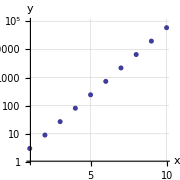
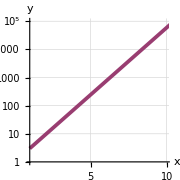
-Graphics-
图5-8 单对数纸 离散列表-Graphics-
图5-9 单对数纸 连续函数

```mathematica
Clear["Global`*"]
fun1[x_]:=3^x;
SetOptions[{ListLogPlot,LogPlot,ListLogLogPlot,LogLogPlot},AspectRatio->1,GridLinesStyle->{ColorData[1,1],PointSize[0.1]},Frame->False,ImageSize->180,MeshStyle->Directive[PointSize[0.001]],AxesLabel->{Style["x",Italic],Style["y",Italic]}];
g1=Column[{ListLogPlot[Table[fun1[x],{x,1,500}],PlotStyle->{ColorData[1,1],PointSize[0.02]},PlotRange->{{1,10},{1,10^5}}],Text@Style["图5-8 单对数纸 离散列表"]},Alignment->Center];
g2=Column[{LogPlot[fun1[x],{x,1,500},PlotStyle->{ColorData[1,2],Thickness[0.015]},PlotRange->{{1,10},{1,10^5}}],
Text@Style["图5-9 单对数纸 连续函数"]},Alignment->Center];
Row[{g1,g2}]
```

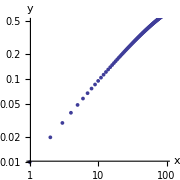
-Graphics-
图5-10 双对数纸 离散

```mathematica
fun2[x_]:=1-Exp[-x/100];
g3=Column[{ListLogLogPlot[Table[fun2[x],{x,1,500}],PlotStyle->{ColorData[1,1],PointSize[0.015]},
PlotRange->{{1,100},{0.01,0.5}}],
Text@Style["图5-10 双对数纸 离散"]},Alignment->Center]
```

```mathematica
(*韦伯模型用双对数纸画是一条直线,α是截距，β是斜率*)
```

```mathematica
Clear["Global`*"]
medianRank[number_]:=Table[N[((i-0.3175)/(number+0.365))],{i,1,number}];
data={118.80,87.32,58.50,249.13,198.28};
n1=medianRank[5]
```

{0.127213,0.313607,0.5,0.686393,0.872787}

表5-3 实验数据的预处理数据列表
No. | L(h) | x=LogL | R(%) | F=R/100 | y=loglog[1/(1-F)]
1 | 58.50 | 1.7672 | 12.72 | 0.1272 | -1.2285
2 | 87.32 | 1.9411 | 31.36 | 0.3136 | -0.7867
3 | 118.80 | 2.0748 | 50.00 | 0.5000 | -0.5214
4 | 198.28 | 2.2973 | 68.64 | 0.6864 | -0.2979
5 | 249.13 | 2.3964 | 87.28 | 0.8728 | -0.0480

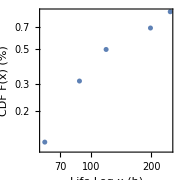

```mathematica
datatable={Range[5],Sort[data],Log10@Sort[data],100medianRank[5],medianRank[5],Log10[Log10[1/(1-medianRank[5])]]};
table=Grid[Prepend[Map[{#[[1]],NumberForm[#[[2]],{5,2}],NumberForm[#[[3]],{5,4}],
NumberForm[#[[4]],{5,2}],NumberForm[#[[5]],{5,4}],
NumberForm[#[[6]],{5,4}]}&,Transpose[datatable]],
{"No.",Row[{Style["L",Italic],"(",Style["h",Italic],")"}],
Row[{Style["x",Italic],"=Log",Style["L",Italic]}],
Row[{Style["R",Italic],"(",Style["%",Italic],")"}],
Row[{Style["F",Italic],"=",Style["R/100",Italic]}],
Row[{Style["y",Italic],"=",Style["loglog[1/(1-F)]",Italic]}]}],
Frame->All,Background->{{LightGray,LightYellow,LightYellow,LightGreen,LightGreen,LightGreen},None}];
Column[{Text@Style["表5-3 实验数据的预处理数据列表"],table},Alignment->Center]
pointdata=Transpose[{datatable[[2]],datatable[[5]]}];
g1=ListLogLogPlot[pointdata,Joined->False,Mesh->All,Frame->True,FrameLabel->{"Life Log x (h)","CDF F(x) (%)"},PlotStyle->{PointSize[0.02]}]
```

```mathematica
logdata=Transpose[{datatable[[3]],datatable[[6]]}];
lsf[data_List]:=Module[{matrix,argb,a,b},matrix=Transpose[{Table[1,{Length[data]}],Transpose[data][[1]]}];
argb=Transpose[data][[2]];
{b,a}=LeastSquares[matrix,argb]];
{b,a}=lsf[logdata];
{α,β}={a,1/((N[1/Log10[E]]*10^b)^(1/a))};
CDF[WeibullDistribution[α,β],x]
```

Piecewise[{{1-ⅇ^(-0.000131969 x^1.74923), x>0}, {0, True}}]

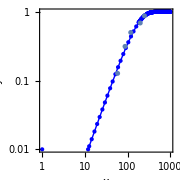

```mathematica
modelplot=LogLogPlot[CDF[WeibullDistribution[α,β],x],{x,1,1000},Mesh->All,MeshStyle->{Blue,PointSize[Tiny]},AspectRatio->1,GridLines->Automatic,ImageSize->180,
Frame->True,PlotStyle->{Blue,Thick},PlotRange->{{1,1000},{0.01,1}}];
Show[{modelplot,g1}]
```

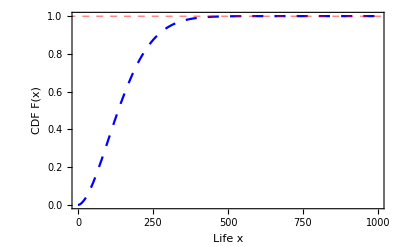

```mathematica
CDFplot=Plot[CDF[WeibullDistribution[α,β],x],{x,0,1000},Frame->True,PlotStyle->{Blue,Dashing[0.02]},FrameLabel->{"Life x","CDF F(x)"},GridLines->{None,{1}},GridLinesStyle->Directive[Red,Dashed]]
```

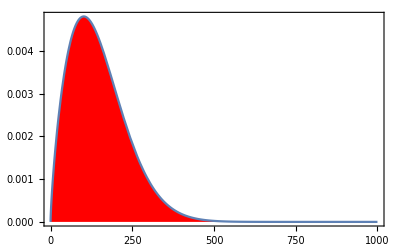

```mathematica
PDFplot=Plot[PDF[WeibullDistribution[α,β],x],{x,0,1000},Filling->Axis,FillingStyle->Red,Frame->True]
```

```mathematica
FindRoot[0.1==CDF[WeibullDistribution[α,β],x],{x,50}][[1]][[2]]
```

45.6176

```mathematica
(*------------------------整体的一个演示代码-------------------*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*First,生成随机数作为初始化数据*)
lifedata[seed_,maxlife_,number_]:=Flatten[Sort[SeedRandom[seed];RandomReal[{1,maxlife},{number,1}]]];
(*计算中间秩*)
medianRank[number_]:=Table[N[((i-0.3175)/(number+0.365))],{i,1,number}];
testtable[seed_,maxlife_,number_]:=With[{life=lifedata[seed,maxlife,number],medianRank=medianRank[number]},{Range[number],life,Log10@life,100*medianRank,medianRank,Log10[Log10[1/(1-medianRank)]]}];
(*定义表格格式和表头*)
tablestyle[seed_,maxlife_,number_]:=Grid[Prepend[Map[{#[[1]],NumberForm[#[[2]],{5,2}],NumberForm[#[[3]],{5,4}],
NumberForm[#[[4]],{5,2}],NumberForm[#[[5]],{5,4}],
NumberForm[#[[6]],{5,4}]}&,Transpose[testtable[seed,maxlife,number]]],
{"No.",Row[{Style["L",Italic],"(",Style["h",Italic],")"}],
Row[{Style["x",Italic],"=Log",Style["L",Italic]}],
Row[{Style["R",Italic],"(",Style["%",Italic],")"}],
Row[{Style["F",Italic],"=",Style["R/100",Italic]}],
Row[{Style["y",Italic],"=",Style["loglog[1/(1-F)]",Italic]}]}],
Frame->All,Background->{{LightGray,LightYellow,LightYellow,LightGreen,LightGreen,LightGreen},None}];
(*定义最小二乘法*)
lsf[logtable_List]:=Module[{matrix,argb,a,b,β,α},matrix=Transpose[{Table[1,{Length[logtable]}],Transpose[logtable][[1]]}];
argb=Transpose[logtable][[2]];
{b,a}=LeastSquares[matrix,argb];
{α,β}={a,1/(N[1/Log10[E]]*10^b)^(1/a)}];
(*第一张图是实验数据点，第二张画拟合后的曲线函数*)
listlogplot[points_List,maxlife_]:=ListLogPlot[points,MeshStyle->PointSize[Tiny],PlotStyle->{PointSize[Tiny],ColorData[1,1]}];
loglogplot[α_,β_,maxlife_]:=LogLogPlot[CDF[WeibullDistribution[α,β],x],{x,1,maxlife},PlotStyle->{ColorData[1,2],Thickness[0.015]}];
combineplot[α_,β_,points_List,maxlife_]:=Show[{listlogplot[points,maxlife],loglogplot[α,β,maxlife]},ImagePadding->25];
(*定义韦伯分布函数和绘图*)
distributionplot[fun_,α_,β_,maxlife_]:=Plot[If[fun,CDF,PDF][WeibullDistribution[α,β],x],{x,1,maxlife},PlotLabel->Row[{"α","=",NumberForm[α,{4,2}],";","β","=",NumberForm[β,{4,2}]}],Filling->If[fun,None,0],PlotStyle->Thick,Frame->True,Axes->False,ImageSize->{170,110},ImagePadding->{{50,7},{35,5}},
FrameLabel->{Row[{"lifetime",Style["L",Italic]}],Row[{"occurrence",If[fun,"CDF","PDF"],Style[If[fun,"F","f"],Italic],"(",Style["x",Italic],")"}]}];
(*操控上面的函数*)
Manipulate[Module[{data,grid,loglogdata,pointdata,α,β},data=testtable[seed,maxlife,number];grid=tablestyle[seed,maxlife,number];
loglogdata=Transpose[{data[[3]],data[[6]]}];
pointdata=Transpose[{data[[2]],data[[5]]}];
{α,β}=lsf[loglogdata];
Grid[{{Pane[Text@grid,ImageSize->{230,145},ImageSizeAction->"ShrinkToFit"],combineplot[α,β,pointdata,maxlife]},{distributionplot[True,α,β,maxlife],distributionplot[False,α,β,maxlife]}},Alignment->Left]],{{seed,1,"new random test"},1,10^4,1,Appearance->"Labeled"},
{{maxlife,10^3,"maxmium lifetime"},
10^3,10^4,10^3,Appearance->"Labeled"},{{number,10,"specimen number"},5,10,1,Appearance->"Labeled"},
ControlPlacement->Top,
TrackedSymbols->Manipulate,SaveDefinitions->True]
```